## Picard’s iterations for dy/dx = f(x,y), y(t_0)=y_0

1+x

1+x+x^2+x^3/3

1+x+x^2+x^3+(2 x^4)/3+x^5/3+x^6/9+x^7/63

1+x+x^2+x^3+x^4+(13 x^5)/15+(2 x^6)/3+(29 x^7)/63+(71 x^8)/252+(86 x^9)/567+(22 x^10)/315+(5 x^11)/189+x^12/126+x^13/567+x^14/3969+x^15/59535

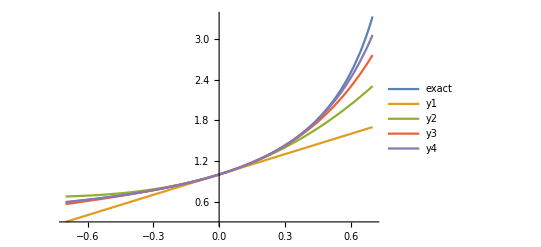

```mathematica
f[x_,y_]:=y^2;
y0=1;
t0=0;
exact[x_]:=1/(1-x);

y1[x_]=y0+Integrate[f[t,y0],{t,t0,x}]
y2[x_]=y0+Integrate[f[t,y1[t]],{t,t0,x}]
y3[x_]=y0+Integrate[f[t,y2[t]],{t,t0,x}]
y4[x_]=y0+Integrate[f[t,y3[t]],{t,t0,x}]

Plot[{exact[x],y1[x],y2[x],y3[x],y4[x]},{x,-.7,.7},PlotLegends->{"exact","y1","y2","y3","y4"}]
```